```mathematica
Integrate[Exp[1-θ]/(Exp[1]-2)θ, {θ,0,1}]
```

1

```mathematica
Probability[a<=τ&&a+b>τ,{a\[Distributed]ExponentialDistribution[λ],b\[Distributed]ExponentialDistribution[λ],c\[Distributed]ExponentialDistribution[λ]}]
```

Piecewise[{{ⅇ^(-λ τ) λ τ, τ≥0}, {0, True}}]

```mathematica
Probability[a+b<=τ&&a+b+c>τ,{a\[Distributed]ExponentialDistribution[λ],b\[Distributed]ExponentialDistribution[λ],c\[Distributed]ExponentialDistribution[λ]}]
```

Piecewise[{{1/2 ⅇ^(-λ τ) λ^2 τ^2, τ≥0}, {0, True}}]

```mathematica
Probability[a+b+c<=1&&a+b+c+d>1,{a\[Distributed]ExponentialDistribution[λ],b\[Distributed]ExponentialDistribution[λ],c\[Distributed]ExponentialDistribution[λ],d\[Distributed]ExponentialDistribution[λ]}]
```

1/6 ⅇ^-λ λ^3

```mathematica
Probability[a+b+c+d<=1&&a+b+c+d+e>1,{a\[Distributed]ExponentialDistribution[λ],b\[Distributed]ExponentialDistribution[λ],c\[Distributed]ExponentialDistribution[λ],d\[Distributed]ExponentialDistribution[λ],e\[Distributed]ExponentialDistribution[λ]}]
```

1/24 ⅇ^-λ λ^4

```mathematica
f[n_,λ_,t_]:=1/Factorial[n] Exp[-λ t](λ t)^n
```

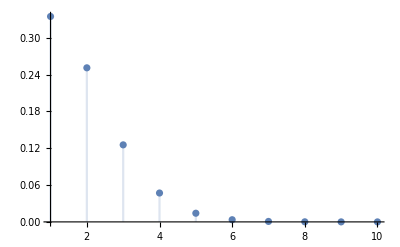

```mathematica
DiscretePlot[f[n,3,0.5],{n,1,10}]
```

```mathematica
Sum[f[n,λ,t],{n,0,∞}]
```

1

```mathematica
Plot[n f[n,3,t],{n,1,10}]
```

## Determining mean

```mathematica
Integrate[(1-CDF[GammaDistribution[n0,1/λ],t]),{t,0,tprimed}]
```

Integrate::pwrl: Unable to prove that integration limits {0,tprimed} are real. Adding assumptions may help.

$Aborted

```mathematica
m[t_,n0_,λ_]:=n0-λ NIntegrate[(1-CDF[GammaDistribution[n0,1/λ],tprimed]),{tprimed,0,t}]
```

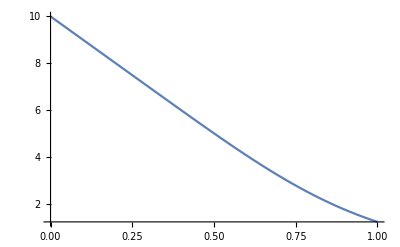

```mathematica
Plot[m[t,10,10],{t,0,1},PlotRange->Full]
```

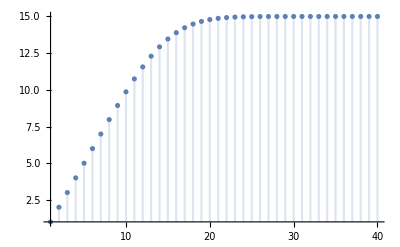

```mathematica
DiscretePlot[n0-m[1,n0,60/4],{n0,1,40},PlotRange->Full]
```

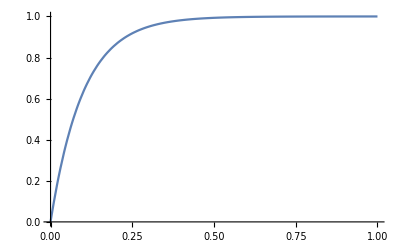

```mathematica
Plot[CDF[GammaDistribution[1,1/10],t],{t,0,1},PlotRange->Full]
```

```mathematica
CDF[GammaDistribution[N0,1/r],t]
```

Piecewise[{{GammaRegularized[N0,0,r t], t>0}, {0, True}}]

## Solve more general equations

```mathematica
meanNumberEaten[N0_,a_,r_,tval_]:=Module[{vars,eqns,init,sol,meanExpr},(*Define state variables*)vars=Flatten[Table[{P[N,1][t],P[N,0][t]},{N,0,N0}]];
(*ODE system with corrected transitions*)eqns=Flatten[Table[{P[N,1]'[t]==-a*N*P[N,1][t]+r*P[N,0][t],P[N,0]'[t]==If[N+1<=N0,a*(N+1)*P[N+1,1][t],0]-r*P[N,0][t]},{N,0,N0}]];
(*Initial conditions*)init=Flatten[Table[{If[N==N0,P[N,0][0]==1,P[N,0][0]==0],P[N,1][0]==0},{N,0,N0}]];
(*Solve the ODEs numerically*)sol=NDSolveValue[Join[eqns,init],Table[{P[N,1][t],P[N,0][t]},{N,0,N0}],{t,0,tval}];
(*Compute mean at time tval using evaluated solution*)meanExpr=Sum[N*(sol[[N+1,1]]+sol[[N+1,2]]/. t->tval),{N,0,N0}];
N0-meanExpr]
```

```mathematica
N0=3;
Flatten[Table[{If[N==N0,P[N,0][0]==1,P[N,1][0]==0],P[N,1][0]==0},{N,0,N0}]]
```

{P[0,1][0]==0,P[0,1][0]==0,P[1,1][0]==0,P[1,1][0]==0,P[2,1][0]==0,P[2,1][0]==0,P[3,0][0]==1,P[3,1][0]==0}

```mathematica
ClearAll["Global`*"]
```

```mathematica
meanNumberEaten[N0,10.0,10,1]
```

2.97773

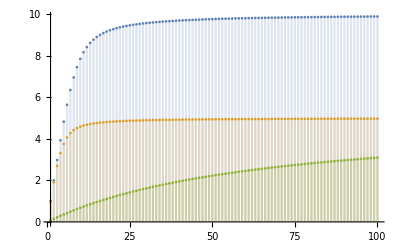

```mathematica
DiscretePlot[{meanNumberEaten[N0,10.0,10,1],meanNumberEaten[N0,10,5,1],meanNumberEaten[N0,0.1,5,1]},{N0,1,100},PlotRange->{{Automatic},{0,N0+1}}]
```

```mathematica
N0=2;
r=0;
Flatten[Table[{P[N,1]'[t]==-a*N*P[N,1][t]+r*P[N,0][t],P[N,0]'[t]==a*(N+1)*If[N+1<=N0,P[N+1,1][t],0]-r*P[N,0][t]},{N,0,3}]]
```

{P[0,1]'[t]==0,P[0,0]'[t]==a P[1,1][t],P[1,1]'[t]==-a P[1,1][t],P[1,0]'[t]==2 a P[2,1][t],P[2,1]'[t]==-2 a P[2,1][t],P[2,0]'[t]==0,P[3,1]'[t]==-3 a P[3,1][t],P[3,0]'[t]==0}

```mathematica
meanApproxHigha[N0_,r_,tval_]:=r tval -  r NIntegrate[CDF[GammaDistribution[N0,1/r],tprimed],{tprimed,0,tval}]
```

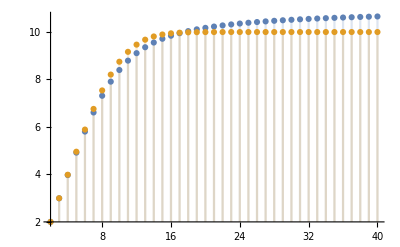

```mathematica
Show[DiscretePlot[{meanNumberEaten[N0,10.0,10,1],meanApproxHigha[N0,10,1]},{N0,2,40},PlotRange->{{Automatic},{0,N0+1}}]]
```

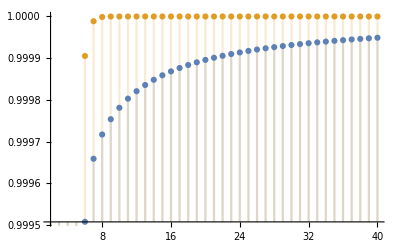

```mathematica
Show[DiscretePlot[{meanNumberEaten[N0,1000.0,1,1],meanApproxHigha[N0,1,1]},{N0,2,40},PlotRange->{{Automatic},{0,N0+1}}]]
```